```mathematica
(* 未经作者同意请不要复制或转载本文任何内容 *)
(* @By wuwc *)
(* @EMail: brucecen2@gmail.com *)
```

```mathematica
(*Join two lists*)
fruits={apples, oranges};
veggies={cucumbers,squash};
all=Join[fruits,veggies]
```

{apples,oranges,cucumbers,squash}

```mathematica
(*Sort*)
```

```mathematica
Sort[all]
```

{apples,cucumbers,oranges,squash}

```mathematica
squares=Table[i^2,{i,10,1,-1}]
```

{100,81,64,49,36,25,16,9,4,1}

```mathematica
new=Sort[squares]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
newer=Sort[new,Greater]
```

{100,81,64,49,36,25,16,9,4,1}

```mathematica
(*Matrix*)
```

```mathematica
data={{0,10},{1,25},{2,50}}
```

{{0,10},{1,25},{2,50}}

```mathematica
data//TableForm
```

0 | 10
1 | 25
2 | 50

```mathematica
data//MatrixForm
```

(0 | 10
1 | 25
2 | 50)

```mathematica
Transpose[data]
```

{{0,1,2},{10,25,50}}

```mathematica
Transpose[data]//TableForm
```

0 | 10
1 | 25
2 | 50

```mathematica
Transpose[data]//MatrixForm
```

(0 | 1 | 2
10 | 25 | 50)

```mathematica
Clear[data]
```

```mathematica
data={{0,0.01},{1000,0.00625},{1800,0.00476},{2800,0.0037},{3600,0.00313},{4400,0.00270},{5200,0.00241},{6200,0.00208}}(*Product*)
```

{{0,0.01},{1000,0.00625},{1800,0.00476},{2800,0.0037},{3600,0.00313},{4400,0.0027},{5200,0.00241},{6200,0.00208}}

```mathematica
TableForm[data,TableHeadings->{None,{"time (s)","[A}, M"}}]
```

time (s) | [A}, M
0 | 0.01
1000 | 0.00625
1800 | 0.00476
2800 | 0.0037
3600 | 0.00313
4400 | 0.0027
5200 | 0.00241
6200 | 0.00208

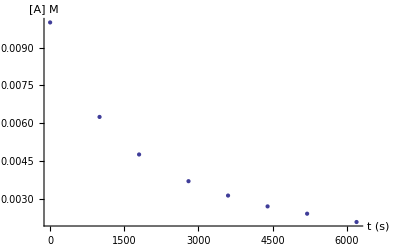

```mathematica
ListPlot[data,AxesLabel->{"t (s)", "[A] M"}]
```

```mathematica
(*reactant order*)
(*1st order: Subscript[ln[A], t]=Subscript[ln[A], 0]-kt*)
(*2nd order: 1/[A]_t=1/[A]_0+kt*)
```

```mathematica
(*Copy that matrix to new matrix*)
newdata=data;
(*All rows in 2nd data*)
newdata[[All,2]]=Log[data[[All,2]]];
newdata//TableForm
```

0 | -4.60517
1000 | -5.07517
1800 | -5.34751
2800 | -5.59942
3600 | -5.76672
4400 | -5.9145
5200 | -6.02813
6200 | -6.17539

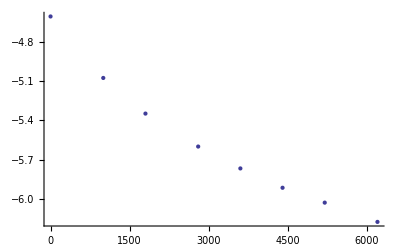

```mathematica
ListPlot[newdata]
```

0 | 100.
1000 | 160.
1800 | 210.084
2800 | 270.27
3600 | 319.489
4400 | 370.37
5200 | 414.938
6200 | 480.769

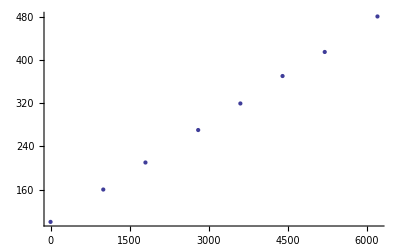

```mathematica
newdata=data;
newdata[[All,2]]=1/data[[All,2]];
newdata//TableForm
ListPlot[newdata]
```

```mathematica
(* Fit data *)
```

```mathematica
(* data:{Subscript[x, i],Subscript[y, i]}
fitting function: f(x)
χ^2=∑_i ((|Subscript[r, i]|)_j)^2, Subscript[y, i]=f(Subscript[x, i])-Subscript[y, i] *)
```

```mathematica
(* Linear not parameters
f(x)=mx+b linear in m,x,b
=ax+bx^2 linear in a,b
=aln(bx) linear in a, but not in b
=a ln(b)+a ln(x)*)
(*f(x)=a cos(bx) linear in a, not b*)
```

```mathematica
y[x_]:=2*x+3;
mydata=Table[{x,y[x]},{x,-1,5}]
```

{{-1,1},{0,3},{1,5},{2,7},{3,9},{4,11},{5,13}}

```mathematica
(* y(x) = b + mx *)
(*        1    x *)
```

```mathematica
fy[x_]=Fit[mydata,{1,x},x]
```

3.+2. x

```mathematica
fy[1]
```

5.

```mathematica
mydata=Table[{x,y[x]+RandomReal[{-1,1}]},{x,-1,5}]
```

{{-1,0.37508},{0,2.04218},{1,4.35376},{2,7.38168},{3,9.99196},{4,11.4572},{5,13.0017}}

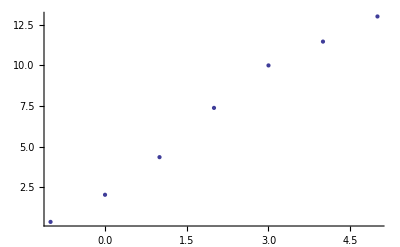

```mathematica
dataplot=ListPlot[mydata]
```

```mathematica
fitdata=Fit[mydata,{1,x},x]
```

2.48993+2.22672 x

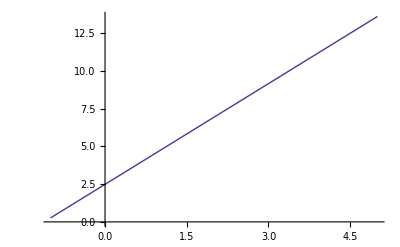

```mathematica
fitplot=Plot[fitdata,{x,-1,5}]
```

```mathematica
(* Put them in one show *)
```

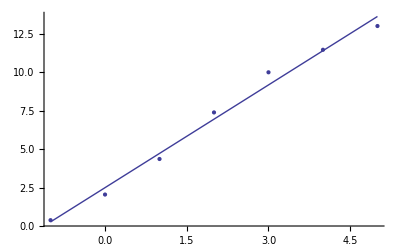

```mathematica
Show[dataplot,fitplot]
```